```mathematica
(* Need to get the notes of the scales*)
(*Need to define the particles, fermions verus bosons*) 
(*create mapping*)
(*define function that maps graph to music*)
An[n_]:=EmitSound[SoundNote["A", n, "Violin"]]
```

```mathematica
Bn[m_]:=EmitSound[SoundNote["B", m, "Violin"]]
As[m1_]:=EmitSound[SoundNote["ASharp", m1, "Violin"]]
Cn[m2_]:=EmitSound[SoundNote["C", m2, "Violin"]]
Cs[m3_]:=EmitSound[SoundNote["CSharp", m3, "Violin"]]
Dn[m4_]:=EmitSound[SoundNote["D", m4, "Violin"]]
Ds[m5_]:=EmitSound[SoundNote["DSharp", m5, "Violin"]]
En[m6_]:=EmitSound[SoundNote["E", m6, "Violin"]]
Fn[m7_]:=EmitSound[SoundNote["F", m7, "Violin"]]
Fs[m8_]:=EmitSound[SoundNote["FSharp", m8, "Violin"]]
Gn[m9_]:=EmitSound[SoundNote["G", m9, "Violin"]]
Gs[m10_]:=EmitSound[SoundNote["GSharp", m10, "Violin"]]
```

```mathematica
HotCrossBuns:= Fs[1]+En[1]+Dn[1]+ Fs[1]+En[1]+Dn[1]+Dn[1]+Dn[1]+Dn[1]+Dn[1]+En[1]+En[1]+En[1]+En[1]+ Fs[1]+En[1]+Dn[1]
```

```mathematica
ChrS:={An, As, Bn, Cn, Cs, Dn, Ds, En, Fn, Fs, Gn, Gs}
```

```mathematica
(*Watch the chords while I define the relations*)
DimSecond[a_]:=If[a<12, a+1, 1];
Second[b_]:=If[b<11, b+2,   1+Mod[b+1, 12]];
DimThird[c_]:=If[c<10, c+3, 1+Mod[c+2, 12]];
Third[d_]:=If[d<9, d+4, 1+Mod[d+3, 12]];
Fourth[e_]:=If[e<8, e+5, 1+Mod[e+4, 12]];
DimFifth[f_]:=If[f<7, f+6, 1+Mod[f+5, 12]];
Fifth[g_]:=If[g<6, g+7, 1+Mod[g+6, 12]];
DimSixth[h_]:=If[h<5, h+8, 1+Mod[h+7, 12]];
Sixth[i_]:=If[i<4, i+9, 1+Mod[i+8, 12]];
DimSeventh[j_]:=If[j<3, j+10, 1+Mod[i+9, 12]];
Seventh[k_]:=If[k<2; k+11, 1+Mod[i+10, 12]];

(*These are the generic relations for the scales*)

(*This is the rule for a single group/chord*)
NoNeut[l_]:={ChrS⟦l⟧, ChrS⟦Third[l]⟧, ChrS⟦Fifth[l]⟧}
```

```mathematica
(*This is the group of the nine fermions w/out neutrinos*)
BaseGroup[m_,n_, o_]={NoNeut[m], NoNeut[n], NoNeut[o]}
```

Part::pkspec1: The expression m cannot be used as a part specification.

Part::pkspec1: The expression If[m<9,m+4,1+Mod[m+3,12]] cannot be used as a part specification.

Part::pkspec1: The expression If[m<6,m+7,1+Mod[m+6,12]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦m⟧,{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[m<9,m+4,1+Mod[m+3,12]]⟧,{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[m<6,m+7,1+Mod[m+6,12]]⟧},{{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦n⟧,{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[n<9,n+4,1+Mod[n+3,12]]⟧,{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[n<6,n+7,1+Mod[n+6,12]]⟧},{{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦o⟧,{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[o<9,o+4,1+Mod[o+3,12]]⟧,{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[o<6,o+7,1+Mod[o+6,12]]⟧}}

```mathematica
NotesLeftOver[p_, q_, r_]:=Complement[ChrS, Flatten[BaseGroup[p, q, r]]]
```

```mathematica
NotesLeftOver[1,2,3]
```

{Cn,Gn,Gs}

```mathematica
L0=Array[NotesLeftOver, {12, 12, 12}]
```

{{{{As,Bn,Cn,Dn,Ds,Fn,Fs,Gn,Gs},{Bn,Cn,Ds,Fs,Gn,Gs},{As,Cn,Dn,Fn,Gn,Gs},{As,Bn,Dn,Ds,Fn,Fs,Gs},{As,Bn,Cn,Dn,Ds,Fs,Gn},{As,Bn,Cn,Ds,Fn,Gn,Gs},{Bn,Cn,Dn,Fn,Fs,Gs},{As,Cn,Dn,Ds,Fn,Fs,Gn},{As,Bn,Dn,Ds,Fs,Gn,Gs},{Bn,Cn,Dn,Ds,Fn,Gn,Gs},{As,Cn,Ds,Fn,Fs,Gs},{As,Bn,Dn,Fn,Fs,Gn}},10,{{As,Bn,Dn,Fn,Fs,Gn},{Bn,Fs,Gn},{As,Dn,Fn,Gn},{As,Bn,Dn,Fn,Fs},4,{As,Bn,Dn,Fs,Gn},{Bn,Dn,Fn,Gn},{As,Fn,Fs},{As,Bn,Dn,Fn,Fs,Gn}}},10,{1}}
 |  |  |  |

```mathematica
Select[Flatten[L0, 2], Length[#]≤3 &]
```

{{Cn,Gn,Gs},{Bn,Fs,Gn},{Cn,Gn,Gs},{As,Fn,Fs},{Bn,Fs,Gn},{As,Fn,Fs},{Cn,Gn,Gs},{Bn,Fs,Gn},{Cn,Gn,Gs},{An,Cs,Gs},{An,Cs,Gs},{Bn,Fs,Gn},{Cn,Gn,Gs},{Cn,Gn,Gs},{An,Cs,Gs},{An,Cs,Gs},{An,As,Dn},{An,As,Dn},{An,Cs,Gs},{An,Cs,Gs},{An,As,Dn},{An,As,Dn},{As,Bn,Ds},{As,Bn,Ds},{An,As,Dn},{An,As,Dn},{As,Bn,Ds},{As,Bn,Ds},{Bn,Cn,En},{Bn,Cn,En},{As,Bn,Ds},{As,Bn,Ds},{Bn,Cn,En},{Bn,Cn,En},{Cn,Cs,Fn},{Cn,Cs,Fn},{Bn,Cn,En},{Bn,Cn,En},{Cn,Cs,Fn},{Cn,Cs,Fn},{Cs,Dn,Fs},{Cs,Dn,Fs},{Cn,Cs,Fn},{Cn,Cs,Fn},{Cs,Dn,Fs},{Cs,Dn,Fs},{Dn,Ds,Gn},{Dn,Ds,Gn},{Cs,Dn,Fs},{Cs,Dn,Fs},{Dn,Ds,Gn},{Dn,Ds,Gn},{Ds,En,Gs},{Ds,En,Gs},{Dn,Ds,Gn},{Dn,Ds,Gn},{Ds,En,Gs},{Ds,En,Gs},{An,En,Fn},{An,En,Fn},{As,Fn,Fs},{Ds,En,Gs},{Ds,En,Gs},{An,En,Fn},{As,Fn,Fs},{An,En,Fn},{Bn,Fs,Gn},{As,Fn,Fs},{Bn,Fs,Gn},{An,En,Fn},{As,Fn,Fs},{An,En,Fn}}

```mathematica
inlistindex=1
InList={{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},}
For[i=1, i≤10, i++, For[ j=i+1, j≤Length[L0⟦i⟧], j++, For[k=j+1, k≤Length[L0⟦i,j⟧], k++, If[Length[L0⟦i,j,k⟧]≤3, InList⟦inlistindex⟧={i, j,k}; inlistindex++;]]]]
```

1

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},Null}

```mathematica
InList=InList⟦1;;12⟧
```

{{1,2,3},{1,2,12},{1,11,12},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12}}

```mathematica
inlistindex=1;
NotesLeft=InList
For[i=1, i≤10, i++,
 For[ j=i+1, j≤Length[L0⟦i⟧], j++, For[k=j+1, k≤Length[L0⟦i,j⟧], k++, If[Length[L0⟦i,j,k⟧]≤3, NotesLeft⟦inlistindex⟧=L0⟦i,j,k⟧; inlistindex++;]]]]
```

{{1,2,3},{1,2,12},{1,11,12},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12}}

```mathematica
NotesLeft
```

{{Cn,Gn,Gs},{Bn,Fs,Gn},{As,Fn,Fs},{An,Cs,Gs},{An,As,Dn},{As,Bn,Ds},{Bn,Cn,En},{Cn,Cs,Fn},{Cs,Dn,Fs},{Dn,Ds,Gn},{Ds,En,Gs},{An,En,Fn}}

```mathematica
Is2=RandomWord[12]
For[i=1, i≤3, i++, If[Second[InList⟦#index1, i⟧]==NotesLeft⟦#index1, i⟧, Is2⟦#index1, i⟧="b", Is2⟦#index1, i⟧="a"]] & @ <|"index1"-> Range[12], "index2"->  Range[3], "index3"-> Range[3]|>
```

{tiled,whether,doddle,biochemical,unobserved,chop,fixative,misconstrue,rivulet,require,uncultured,contraindicate}

```mathematica
Is2
```

{tiled,whether,doddle,biochemical,unobserved,chop,fixative,misconstrue,rivulet,require,uncultured,contraindicate}

```mathematica
Is2
```

{{1,2,3},{1,2,12},{1,11,12},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12}}

```mathematica
Is2
```

{{1,2,3},{1,2,12},{1,11,12},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12}}

```mathematica
2to2.F
```

```mathematica
$LoadFeynArts=True;
<<FeynCalc';
```

Get::noopen: Cannot open FeynCalc.

```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"] InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True];
$LoadFeynArts=True;
<<FeynCalc';
```

Downloading FeynCalc from https://github.com/FeynCalc/feyncalc/archive/master.zip ...done! 
FeynCalc zip file was saved to C:\Users\Silas Grossberndt\AppData\Local\Temp\m-c0deb267-b9b4-4b9b-bc8a-8899c45016b1.
Extracting FeynCalc zip file to C:\Users\Silas Grossberndt\AppData\Local\Temp\m-c0deb267-b9b4-4b9b-bc8a-8899c45016b1.dir ...done! 
Recognizing the directory structure...done! 
Copying FeynCalc to C:\Users\Silas Grossberndt\AppData\Roaming\Mathematica\Applications\FeynCalc ...done! 
Setting up the help system ... Setting up the format type of new output cells ... done! 
Creating the configuration file ... done! 
Downloading FeynArts from https://github.com/FeynCalc/feynarts-mirror/archive/master.zip ...done! 
FeynArts zip file was saved to C:\Users\Silas Grossberndt\AppData\Local\Temp\m-dc7f3573-b439-4bde-bc6c-e4cea2b1b9d3.
Extracting FeynArts zip file to C:\Users\Silas Grossberndt\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts ...done! 
Copying FeynArts to C:\Users\Silas Grossberndt\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts ...done! 

Installation complete! Loading FeynCalc ... 
Patching FeynArts... done!

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

F::shdw: Symbol F appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.11 (11 Apr 2019) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynCalc::context: FeynCalc has detected strange objects in the Global or FeynCalc contexts.

New lowercase objects in the Global context: {Global`F}

Get::noopen: Cannot open FeynCalc.

```mathematica
2to2.F
```

2 to2.F

```mathematica
CreateTopologies[0, 2->2]
```

TopologyList(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(5)),Propagator(Incoming)(Vertex(1)(2),Vertex(4)(5)),Propagator(Outgoing)(Vertex(1)(3),Vertex(4)(5)),Propagator(Outgoing)(Vertex(1)(4),Vertex(4)(5))),Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(5)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(6)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6))),Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(6)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(5)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(6)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6))),Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(6)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(5)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6))))

```mathematica
TopologyList[
Topology[2][
Propagator[Incoming][Vertex[1][1], Vertex[3][2]],
Propagator[Outgoing][Vertex[1][3], Vertex[3][2]],
Propagator[Incoming][Vertex[1][4], Vertex[3][5]], 
Propagator[Outgoing][Vertex[1][6], Vertex[3][5]],
Propagator[Internal][Vertex[3][2], Vertex[3][5] ]
]](*
Topology[]
[
Propagator[Incoming][Vertex[1][1], Vertex[3][2], PropagatorGraphics[V[5],Forward, "g"]],
Propagator[Incoming][Vertex[1][3], Vertex[3][4], V[5],PropagatorGraphics[V[5],Forward, "g"]],
Propagator[Internal][Vertex[3][2], Vertex[3][4], PropagatorGraphics[F[2, {3}], ,"\tau"]],
Propagator[Internal] [Vertex[3][2], Vertex[3][5], PropagatorGraphics[F[3, {3}], Backward, "\bar{t}"]],
Propagator[Internal] [Vertex[3][2], Vertex[3][5], PropagatorGraphics[F[3, {3},Forward, "t"]]],

]*)
```

TopologyList(Topology(2)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(2)),Propagator(Incoming)(Vertex(1)(4),Vertex(3)(5)),Propagator(Outgoing)(Vertex(1)(6),Vertex(3)(5)),Propagator(Internal)(Vertex(3)(2),Vertex(3)(5))))

```mathematica
Paint[%]
```

> Top. 1 abde\cbfe\be.m, 0 diagrams

```mathematica
CreateTopologies[0, 2->2];
```

```mathematica
TopologyList[
Topology[2][
Propagator[Incoming][Vertex[1][1], Vertex[4][2], F[2,{1}]],
Propagator[Outgoing][Vertex[1][3], Vertex[4][2]],
Propagator[Incoming][Vertex[1][4], Vertex[4][5]], 
Propagator[Outgoing][Vertex[1][6], Vertex[4][5]],
Propagator[Internal][Vertex[4][2], Vertex[4][5] , V[1]]
]]
```

TopologyList(Topology(2)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(2),F(2,{1})),Propagator(Outgoing)(Vertex(1)(3),Vertex(4)(2)),Propagator(Incoming)(Vertex(1)(4),Vertex(4)(5)),Propagator(Outgoing)(Vertex(1)(6),Vertex(4)(5)),Propagator(Internal)(Vertex(4)(2),Vertex(4)(5),V(1))))

> Top. 1 abde\cbfe\be.m, 0 diagrams

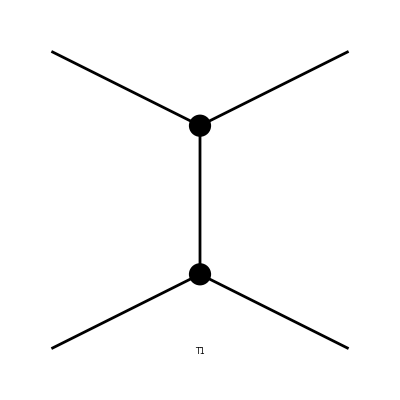

FeynArtsGraphics(2→2)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

FeynArtsGraphics(2→2)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
Paint[%]
```

```mathematica
CreateTopologies[0, 2->6];
TopologyList[
	Topology[2][
		Propagator[Incoming][Vertex[1][1], Vertex[4][2], V[5]],
		Propagator[Incoming][Vertex[1][3], Vertex[4][4], V[5]],
Propagator[Internal][Vertex[4][2], Vertex[4][4] ],
Propagator[Internal][Vertex[4][2], Vertex[4][5]],
Propagator[Internal][Vertex[4][3], Vertex[4][5]],
Propagator[Internal][Vertex[4][5], Vertex[4][6], S[1]],
Propagator[Internal][Vertex[4][6], Vertex[4][7]],
Propagator[Internal][Vertex[4][6], Vertex[4][8]],
Propagator[Outgoing][Vertex[4][7], Vertex[1][9]],
Propagator[Internal][Vertex[4][7], Vertex[4][10], V[3]],
Propagator[Outgoing][Vertex[4][10], Vertex[1][11]],
Propagator[Outgoing][Vertex[4][10], Vertex[1][12]],
Propagator[Outgoing][Vertex[4][8], Vertex[1][13]],
Propagator[Internal][Vertex[4][8], Vertex[4][14], V[3]],
Propagator[Outgoing][Vertex[4][14], Vertex[1][15]],
Propagator[Outgoing][Vertex[4][14], Vertex[1][16]]
]]
```

TopologyList(Topology(2)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(2),V(5)),Propagator(Incoming)(Vertex(1)(3),Vertex(4)(4),V(5)),Propagator(Internal)(Vertex(4)(2),Vertex(4)(4)),Propagator(Internal)(Vertex(4)(2),Vertex(4)(5)),Propagator(Internal)(Vertex(4)(3),Vertex(4)(5)),Propagator(Internal)(Vertex(4)(5),Vertex(4)(6),S(1)),Propagator(Internal)(Vertex(4)(6),Vertex(4)(7)),Propagator(Internal)(Vertex(4)(6),Vertex(4)(8)),Propagator(Outgoing)(Vertex(4)(7),Vertex(1)(9)),Propagator(Internal)(Vertex(4)(7),Vertex(4)(10),V(3)),Propagator(Outgoing)(Vertex(4)(10),Vertex(1)(11)),Propagator(Outgoing)(Vertex(4)(10),Vertex(1)(12)),Propagator(Outgoing)(Vertex(4)(8),Vertex(1)(13)),Propagator(Internal)(Vertex(4)(8),Vertex(4)(14),V(3)),Propagator(Outgoing)(Vertex(4)(14),Vertex(1)(15)),Propagator(Outgoing)(Vertex(4)(14),Vertex(1)(16))))

```mathematica
Print[%]
```

TopologyList(Topology(2)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(2),V(5)),Propagator(Incoming)(Vertex(1)(3),Vertex(4)(4),V(5)),Propagator(Internal)(Vertex(4)(2),Vertex(4)(4)),Propagator(Internal)(Vertex(4)(2),Vertex(4)(5)),Propagator(Internal)(Vertex(4)(3),Vertex(4)(5)),Propagator(Internal)(Vertex(4)(5),Vertex(4)(6),S(1)),Propagator(Internal)(Vertex(4)(6),Vertex(4)(7)),Propagator(Internal)(Vertex(4)(6),Vertex(4)(8)),Propagator(Outgoing)(Vertex(4)(7),Vertex(1)(9)),Propagator(Internal)(Vertex(4)(7),Vertex(4)(10),V(3)),Propagator(Outgoing)(Vertex(4)(10),Vertex(1)(11)),Propagator(Outgoing)(Vertex(4)(10),Vertex(1)(12)),Propagator(Outgoing)(Vertex(4)(8),Vertex(1)(13)),Propagator(Internal)(Vertex(4)(8),Vertex(4)(14),V(3)),Propagator(Outgoing)(Vertex(4)(14),Vertex(1)(15)),Propagator(Outgoing)(Vertex(4)(14),Vertex(1)(16))))